# Beckmann NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
Beckmann`D[u_,α_]:=(ⅇ^(-(-1+1/u^2)/α^2))/(α^2 π u^4)HeavisideTheta[u]
```

```mathematica
Beckmann`σ[u_,α_]:=1/2(u(1+Erf[u/(α √(1-u^2))])+α √(1-u^2)(E^(u^2/(α^2(u^2-1))))/(√Pi))
```

```mathematica
Beckmann`Λ[u_,α_]:=1/2 (-1+(ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) α)/(√π u)+Erf[u/(√(1-u^2) α)])
```

```mathematica
(1+Beckmann`Λ[u,α])u==Beckmann`σ[u,α]//FullSimplify
```

True

```mathematica
(Beckmann`Λ[u,α])u==Beckmann`σ[-u,α]//FullSimplify
```

True

```mathematica
FullSimplify[Beckmann`Λ[u,u/(√(1-u^2) x)],Assumptions->0<u<1&&x>0]
```

1/2 (-1+(ⅇ^(-x^2))/(√π x)+Erf[x])

### shape invariant f(x)

```mathematica
FullSimplify[Beckmann`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0]
```

(ⅇ^(-x^2))/π

### height field normalization

```mathematica
Integrate[2Pi u Beckmann`D[u,α],{u,0,1},Assumptions->0<α<1]
```

1

### distribution of slopes

```mathematica
FullSimplify[Beckmann`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

(ⅇ^(-(p^2+q^2)/α^2))/(π α^2)

```mathematica
Beckmann`P22[p_,q_,α_]:=(ⅇ^(-(p^2+q^2)/α^2))/(π α^2)
```

```mathematica
Integrate[Beckmann`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

```mathematica
Integrate[Beckmann`P22[p,q,α],{q,-Infinity,Infinity},Assumptions->α>0&&Im[p]==0]
```

(ⅇ^(-p^2/α^2))/(√π α)

```mathematica
Beckmann`P2[p_,α_]:=(ⅇ^(-p^2/α^2))/(√π α)
```

### derivation of Λ(u)

```mathematica
FullSimplify[(√(1-u^2))/u Integrate[(q-u/(√(1-u^2)))Beckmann`P2[q,α],{q,u/(√(1-u^2)),Infinity},Assumptions->0<u<1&&0<α<1],Assumptions->0<u<1&&0<α<1]
```

1/2 (-1+(ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) α)/(√π u)+Erf[u/(√(1-u^2) α)])

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

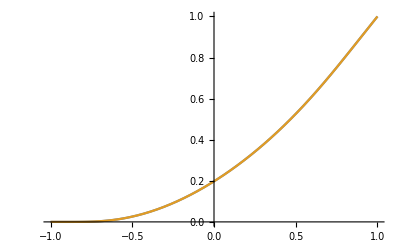

```mathematica
With[{α=.7},
Plot[{
Quiet[NIntegrate[Beckmann`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
Quiet[Beckmann`σ[u,α]]
},{u,-1,1}]
]
```